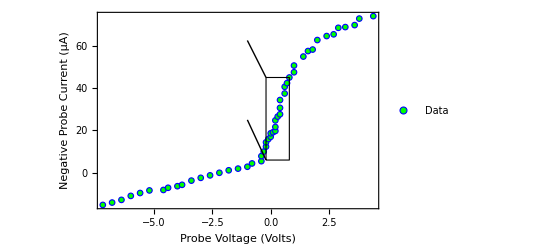

```mathematica
VP = {-7.2,-6.8,-6.4,-6,-5.6,-5.2,-4.6,-4.4,-4,-3.8,-3.4,-3,-2.6,-2.2,-1.8,-1.4,-1,-0.8,-0.4,-0.4,-0.3,-0.2,-0.2,-0.1,0,0,0.1,0.2,0.2,0.2,0.3,0.4,0.4,0.4,0.6,0.6,0.7,0.8,1,1,1.4,1.6,1.8,2,2.4,2.7,2.9,3.2,3.6,3.8,4.4};
IPsat = {15.19507306,14.07073645,12.80421976,10.92158932,9.560285889,8.341162557,8.123851967,7.087750016,6.342560334,5.685605303,3.708188132,2.39427807,1.222548103,0.003424771,-1.168305196,-1.960888243,-2.848258021,-4.405686985,-5.482630223,-7.852298469,-9.986463188,-12.34811606,-14.38603075,-15.92303907,-16.98611374,-18.64488152,-19.13923581,-19.72837683,-21.62411143,-24.75207351,-26.52604866,-27.6365167,-30.66969205,-34.36637452,-37.44039116,-40.61574661,-42.34232839,-45.01677747,-47.47468037,-50.65003582,-54.90233451,-57.5024175,-58.20676589,-62.70258348,-64.58521393,-65.40476969,-68.47878634,-68.82440846,-69.7591716,-72.83318824,-73.99836613};
data = Thread[{VP, -IPsat}];
marker = Graphics[{EdgeForm[{Blue}], FaceForm[Green], Disk[]}];
box1 = Graphics[{EdgeForm[{Thick, Black}], FaceForm[Transparent],Rectangle[{-0.2,6.01},{0.8,45.01}]}];
arrow1 = Graphics[Arrow[{{-3,35},{-.8,0}}]];
plot1 = ListPlot[data, PlotLegends->Placed[{"Data"},{Right, Bottom}], Frame->True, FrameLabel-> {{"Negative Probe Current (μA)",""},{"Probe Voltage (Volts)",""}}, PlotMarkers->{marker, 0.04}, Axes->False];
line1 = Graphics[{Thick,Line[{{-0.2, 6.01},{-1,25}}]}];
line2 = Graphics[{Thick,Line[{{-0.2, 45.01},{-1,62.5}}]}];
plot2=Show[plot1, box1, line1, line2];

VP2 = {-0.2,-0.1,0,0,0.1,0.2,0.2,0.2,0.3,0.4,0.4,0.4,0.6,0.6,0.7,0.8};
logs = {1.157940984,1.202025961,1.230094028,1.270559628,1.281924593,1.295091355,1.334938271,1.393611586,1.423672562,1.441483304,1.486709415,1.536133719,1.573340377,1.608694441,1.626774736,1.653374403};
bestfit[x_]:=0.541 x + 1.2517
data2 = Thread[{VP2, logs}];
plot3 = ListPlot[data2, Frame-> True, FrameLabel->{{"Log(-I_P)  (μA)",""},{"Probe Voltage (Volts)",""}}, Axes->False, PlotMarkers->{marker,0.09}];
plot4 = Plot[bestfit[x],{x,-1,1}, PlotStyle->Directive[Orange]];
text2 = Graphics[Text[Style["y = 0.541 x + 1.2517", Orange,10],{0.2,1.6}]];
plot5 = Show[plot3,plot4, text2, FrameStyle->Directive[Thick]];
final =Magnify[Show[plot2, Epilog-> {Inset[plot5, {-3.7, 40}, Automatic, Scaled[0.65]]}],2]
Export[NotebookDirectory[]<>"../Plots/ElectronDensity.png",final, "PNG"];
Export[NotebookDirectory[]<>"../Plots/ElectronDensity.svg",final, "SVG"];
```